## First Code - Slowest

```mathematica
ClearSystemCache[];

ClearAll[genMatrix, n, list];

genMatrix[n_Integer] := Module[{A, i, j},
(* Error Checking *)
If[n<1,
(Print[Text[Style["ERROR: ", Red, Bold]], Text[Style["Inputted Cell["n",ExpressionUUID->"657bade5-ed02-4611-b178-e6d029ead070"] does not satisfy Cell["n>0",ExpressionUUID->"2a637676-3e26-405b-9227-840c7b509dd6"]!", Red]]];Return[Null])];

(* Generate Matrix *)
A = {Append[ConstantArray[0, n], 1]};
Do[
A = ArrayFlatten[({{A}, {{Table[(j/n)^(n-i), {i, 0, n}]}}})];
, {j, 1, n}];

(* Return result *)
Return[A]
];

Sum[Timing[genMatrix[500]][[1]], {i, 1, 5}]/5
```

3.55452

## Second Code - Slightly faster

```mathematica
ClearSystemCache[];

ClearAll[genMatrix, n, list];

genMatrix[n_Integer] := Module[{A, i, j},
(* Error Checking *)
If[n<1,
(Print[Text[Style["ERROR: ", Red, Bold]], Text[Style["Inputted Cell["n",ExpressionUUID->"adc212f7-a154-440d-9ac7-8699d023e6d4"] does not satisfy Cell["n>0",ExpressionUUID->"8de55849-0e60-4d89-a69d-4b36657dc3eb"]!", Red]]];Return[Null])];

(* Pre-Allocate Matrix *)
A = ConstantArray[0, {n+1, n+1}];

(* Generate Matrix *)
A[[;;,n+1]] = ConstantArray[1, n+1];
A[[n+1]] = ConstantArray[1, n+1];
Do[
A[[j+1,1;;-2]] = Table[(j/n)^i, {i, n, 1, -1}];
, {j, 1, n-1}];

(* Return result *)
Return[A]
];

genMatrix[2] // Inverse // Transpose // MatrixForm
genMatrix[2] // Inverse // MatrixForm

Det[genMatrix[3]]

genMatrix[2] // MatrixForm

((2)!)/3^2
```

(2 | -3 | 1
-4 | 4 | 0
2 | -1 | 0)

(2 | -4 | 2
-3 | 4 | -1
1 | 0 | 0)

4/243

(0 | 0 | 1
1/4 | 1/2 | 1
1 | 1 | 1)

2/9

## Third Code - Even Less Slightly Faster

```mathematica
ClearSystemCache[];

ClearAll[genMatrix, n, list];

genMatrix[n_Integer] := Module[{A, i, j},
(* Error Checking *)
If[n<1,
(Print[Text[Style["ERROR: ", Red, Bold]], Text[Style["Inputted Cell["n",ExpressionUUID->"aa46e41f-c465-4e1a-896f-54ed4de5bba3"] does not satisfy Cell["n>0",ExpressionUUID->"795f049a-f047-41ea-b06f-19e53d702fa2"]!", Red]]];Return[Null])];

(* Pre-Allocate Matrix *)
A = ConstantArray[0, {n+1, n+1}];

(* Generate Matrix *)
A[[;;,n+1]] = ConstantArray[1, n+1];
A[[n+1,1;;-2]] = ConstantArray[1, n];
A[[2;;-2,1;;-2]] = Table[(j/n)^i, {j, 1, n-1, 1}, {i, n, 1, -1}];

(* Return result *)
Return[A]
];

genMatrix[3] // MatrixForm
```

(0 | 0 | 0 | 1
1/27 | 1/9 | 1/3 | 1
8/27 | 4/9 | 2/3 | 1
1 | 1 | 1 | 1)

## Fourth Code - Typically Slower (Don’t Use)

```mathematica
ClearSystemCache[];

ClearAll[genMatrix, n, list];

genMatrix[n_Integer] := Module[{A, i, j},
(* Error Checking *)
If[n<1,
(Print[Text[Style["ERROR: ", Red, Bold]], Text[Style["Inputted Cell["n",ExpressionUUID->"814b62bd-e4f5-42b9-9c1a-97863ac0daa5"] does not satisfy Cell["n>0",ExpressionUUID->"97d2bca7-f8c6-429b-8c27-ed2c5e0af375"]!", Red]]];Return[Null])];

(* Pre-Allocate Matrix *)
A = ConstantArray[0, {n+1, n+1}];

(* Generate Matrix *)
A[[;;,n+1]] = ConstantArray[1, n+1];
A[[n+1,1;;-2]] = ConstantArray[1, n];
If[n>1, (* If matrix is at least 3×3, compute sub-matrix *)
If[n>160, (* ParallelTable is slower for roughly n>160 on M2 Macbook Air *)
A[[2;;-2,1;;-2]] = Table[(j/n)^i, {j, 1, n-1, 1}, {i, n, 1, -1}];
,
A[[2;;-2,1;;-2]] = ParallelTable[(j/n)^i, {j, 1, n-1, 1}, {i, n, 1, -1}];
];
];

(* Return result *)
Return[A]
];

Sum[Timing[genMatrix[3]][[1]], {i, 1, 5}]/5
```

0.0020126

## Mathematical Explanation

First note this in regards to finding piecewise polynomial basis functions on the reference domain [0,1]. The goal is to have these functions add up to 1 (at least on the reference domain) which will evenly contribute from each interpolant node implying a good scheme.

### Example of What is Being Done

Let the reference domain be ζ∈[0,1], and arbitrarily define our piecewise polynomials to be degree n=2. Note that ϕ_i basis functions are 1 at their i^th interpolant node, and 0 at all other interpolant nodes, and piecewise continuous between these nodes. All ϕ_i(ζ) will need to add a midway interpolant node to artificially produce a new root. So we apply the mesh {ζ_0=0, ζ_1=1/2, ζ_2=ζ_n=1} onto our reference domain.

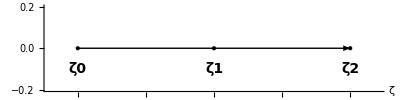

```mathematica
(* Code to be replaced *)
Graphics[{Arrowheads[0.05],Arrow[{{0,0},{1,0}}],PointSize[Large],Point[{0,0}],Point[{0.5,0}],Point[{1,0}],Text[Style["ζ0",Bold,14],{0,-0.1}],Text[Style["ζ1",Bold,14],{0.5,-0.1}],Text[Style["ζ2",Bold,14],{1,-0.1}]},PlotRange->{{-0.1,1.1},{-0.2,0.2}},AspectRatio->1/4,Axes->True,AxesLabel->{"ζ",None}]
```

Finding the proper basis functions, since we have 3 interpolant nodes, we need 3 ϕ_i(ζ) functions. Set up the linearized systems for each such that, for ϕ_0:

ϕ_0(ζ)=aζ^2+bζ+c
ϕ_0(0)=c=1
ϕ_0(1/2)=a/4+b/2+c=0
ϕ_0(1)=a+b+c=0
⇒ (0 | 0 | 1
1/4 | 1/2 | 1
1 | 1 | 1)(a
b
c)=(1
0
0)

For ϕ_1:

ϕ_1(ζ)=αζ^2+βζ+γ
ϕ_1(0)=γ=0
ϕ_1(1/2)=α/4+β/2+γ=1
ϕ_1(1)=a+b+c=0
⇒ (0 | 0 | 1
1/4 | 1/2 | 1
1 | 1 | 1)(α
β
γ)=(0
1
0)

For ϕ_2:

ϕ_2(ζ)=xζ^2+yζ+z
ϕ_2(0)=z=0
ϕ_2(1/2)=x/4+y/2+z=0
ϕ_2(1)=x+y+z=1
⇒ (0 | 0 | 1
1/4 | 1/2 | 1
1 | 1 | 1)(x
y
z)=(0
0
1)

Notice how each ϕ_i has the same system of coefficients in their linearized forms, and the same structure for their unknown vector. That means we can simplify the notation used to obtain the coefficients such that, for ϕ_0 (and plugging in the node values to make generalizing more obvious):

ϕ_0(ζ)=x_0 ζ^2+x_1 ζ+x_2
⇒ (x_0
x_1
x_2)=(ζ_0^2 | ζ_0 | 1
ζ_1^2 | ζ_1 | 1
ζ_2^2 | ζ_2 | 1)^-1(1
0
0)

For ϕ_1:

ϕ_1(ζ)=x_0 ζ^2+x_1 ζ+x_2
⇒ (x_0
x_1
x_2)=(0 | 0 | 1
1/4 | 1/2 | 1
1 | 1 | 1)^-1(0
1
0)

For ϕ_2:

ϕ_2(ζ)=x_0 ζ^2+x_1 ζ+x_2
⇒ (x_0
x_1
x_2)=(0 | 0 | 1
1/4 | 1/2 | 1
1 | 1 | 1)^-1(0
0
1)

To provide an explicit form, we have that:

(0 | 0 | 1
1/4 | 1/2 | 1
1 | 1 | 1)^-1=(2 | -4 | 2
-3 | 4 | -1
1 | 0 | 0)

Now we can easily see the solution to each linearized system. For ϕ_0:

ϕ_0(ζ)=x_0 ζ^2+x_1 ζ+x_2
⇒ (x_0
x_1
x_2)=(2 | -4 | 2
-3 | 4 | -1
1 | 0 | 0)(1
0
0)
⇒ (x_0
x_1
x_2)=(2
-3
1)
⇒ ϕ_0(ζ)=2 ζ^2-3ζ+1

For ϕ_1:

ϕ_1(ζ)=x_0 ζ^2+x_1 ζ+x_2
⇒ (x_0
x_1
x_2)=(2 | -4 | 2
-3 | 4 | -1
1 | 0 | 0)(0
1
0)
⇒ (x_0
x_1
x_2)=(-4
4
0)
⇒ ϕ_1(ζ)=-4 ζ^2+4ζ

For ϕ_2:

ϕ_2(ζ)=x_0 ζ^2+x_1 ζ+x_2
⇒ (x_0
x_1
x_2)=(2 | -4 | 2
-3 | 4 | -1
1 | 0 | 0)(0
0
1)
⇒ (x_0
x_1
x_2)=(2
-1
0)
⇒ ϕ_2(ζ)=2 ζ^2-ζ

Pay special attention to how each right vector we are provided simply has a 1 in the i+1 vector position, or for ϕ_0 there is a 1 in the 1^st vector position and 0 in all others. This means that we already have our coefficients without vector multiplication by simply indexing the matrix elements. So if we generate the coefficient matrix and then invert it, we have all degree n basis polynomials in which ϕ_0’s coefficients are the first column, ϕ_1’s coefficients are the second column, etc.

It was claimed we need these to add up to 1 on the domain. Ensuring this is the case:

ϕ_0(ζ)+ϕ_1(ζ)+ϕ_2(ζ)=(2 ζ^2-3ζ+1)+(-4 ζ^2+4ζ)+(2 ζ^2-ζ)
=(2-4+2)ζ^2+(-3+4-1)ζ+(1+0+0)
=1

Equivalently, we should be able to decompose the inverted matrix into column vectors, add them all up, and obtain (0
0
1), or:

(2 | -4 | 2
-3 | 4 | -1
1 | 0 | 0)
⇒ (2
-3
1)+(-4
4
0)+(2
-1
0)=(0
0
1)

Just for the sake of exemplifying, these 3 basis functions we derived are plotted below:

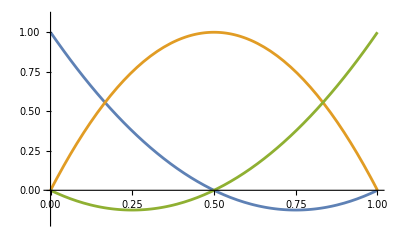

```mathematica
(*Code to be replaced*)
Plot[
{2*ζ^2-3*ζ+1, -4*ζ^2+4*ζ, 2*ζ^2-ζ},
{ζ, 0, 1}, PlotRange->{-0.2, 1.1}]
```

### General proof

We’ve shown the method holds for n=2, and it is trivial for n=1. Now we seek to show the generalized case.

#### Matrix Construction

For degree n, we will have n+1 basis functions, and a n+1×n+1 matrix representing the system. For simplicity, we will use a uniform mesh on the reference domain. Construct the matrix such that:

A=(0 | 0 | 0 | ⋯ | 1
(1/n)^n | (1/n)^(n-1) | (1/n)^(n-2) | ⋯ | 1
(2/n)^n | (2/n)^(n-1) | (2/n)^(n-2) | ⋯ | 1
⋮ | ⋮ | ⋮ | ⋱ | ⋮
(n/n)^n | (n/n)^(n-1) | (n/n)^(n-2) | ⋯ | 1)=(0 | 0 | 0 | ⋯ | 1
(1/n)^n | (1/n)^(n-1) | (1/n)^(n-2) | ⋯ | 1
(2/n)^n | (2/n)^(n-1) | (2/n)^(n-2) | ⋯ | 1
⋮ | ⋮ | ⋮ | ⋱ | ⋮
1 | 1 | 1 | ⋯ | 1)

#### Showing the Matrix is Non-Singular

To show the matrix is non-singular, showing every row is piecewise linearly independent will suffice. This stems from the fact that linear independence among rows (or columns) implies we can row reduce to the identity matrix implying non-singularity since the matrix is guaranteed square. Trivially, the first and last rows are piecewise linearly independent.

To show for the remaining rows, let α be the fractional numerator for a arbitrary “in-between” row, let β be the fractional numerator for a arbitrary “in-between” row such that α≠β. We arbitrarily constrain α,β∈{1, 2, 3, ..., n-1}. Suppose for the sake of contradiction, there exists γ such that:

γ*((α/n)^n | (α/n)^(n-1) | ⋯ | 1)=((β/n)^n | (β/n)^(n-1) | ⋯ | 1)

Because the last elements already agree, we have the constraint that γ=1. But since α≠β, considering the second to last element we just claimed that 1*(α/n)=(β/n) further implying α=β; a contradiction.

Hence by contradiction, all “in-between” rows are piecewise linearly independent. Since the first and last rows were trivial, A has all piecewise linearly independent rows implying A is invertible.

#### Showing the Matrix’s Inverse’s Column Sum is OverVector[e_(n+1)]

For this, we do not need to know the inverse of A since we know A^-1 exists. Note that OverVector[e_i] is an appropriately sized vector that is all 0 except for a 1 in the i^th position. The question we are seeking to prove is as follows:

∑_(i=1)^(n+1) A^-1*OverVector[e_i]=OverVector[e_(n+1)]

Through algebraic manipulation, we can rephrase this question such that:

∑_(i=1)^(n+1) A^-1*OverVector[e_i]=OverVector[e_(n+1)]
⇒ A^-1*∑_(i=1)^(n+1) OverVector[e_i]=OverVector[e_(n+1)]
⇒ AA^-1*∑_(i=1)^(n+1) OverVector[e_i]=A OverVector[e_(n+1)]
⇒ ∑_(i=1)^(n+1) OverVector[e_i]=A OverVector[e_(n+1)]
⇒ (1
1
⋮
1
1)=(0 | 0 | 0 | ⋯ | 1
(1/n)^n | (1/n)^(n-1) | (1/n)^(n-2) | ⋯ | 1
(2/n)^n | (2/n)^(n-1) | (2/n)^(n-2) | ⋯ | 1
⋮ | ⋮ | ⋮ | ⋱ | ⋮
1 | 1 | 1 | ⋯ | 1)(0
0
⋮
0
1)

Here, we can trivially see the statement is true. So this method of deriving piecewise polynomials of degree n holds.

## Application

Here we use our results to show how this can be implemented into a live scheme. Consider if our PDE has the weak left-side form of ∫_a^b ϕ_k'(x)*ϕ_j'(x)ⅆx. This is the standard form used for the ODE -u_xx=f. We will not care about the right side as it’s seen as easier to construct.

Define h=x_k-x_(k-1)=(b-a)/m for all reasonable indices k with the mesh {a=x_0, x_1, ..., x_m=b}. Using the provided code, we can efficiently generate our system, then invert it to obtain our ϕ polynomial coefficients for each ϕ_i. Doing so, consider degree n=3 basis polynomials:

```mathematica
ClearAll[genMatrix, n, list];

genMatrix[n_Integer] := Module[{A, i, j},
(* Error Checking *)
If[n<1,
(Print[Text[Style["ERROR: ", Red, Bold]], Text[Style["Inputted Cell["n",ExpressionUUID->"efcbfef4-6db3-4367-8d88-386b3a71586e"] does not satisfy Cell["n>0",ExpressionUUID->"7cc18c38-7e5e-4494-8530-6ec045834621"]!", Red]]];Return[Null])];

(* Pre-Allocate Matrix *)
A = ConstantArray[0, {n+1, n+1}];

(* Generate Matrix *)
A[[;;,n+1]] = ConstantArray[1, n+1];
A[[n+1,1;;-2]] = ConstantArray[1, n];
A[[2;;-2,1;;-2]] = Table[(j/n)^i, {j, 1, n-1, 1}, {i, n, 1, -1}];

(* Return result *)
Return[A]
];

genMatrix[3] // Inverse // MatrixForm
```

(-9/2 | 27/2 | -27/2 | 9/2
9 | -45/2 | 18 | -9/2
-11/2 | 9 | -9/2 | 1
1 | 0 | 0 | 0)

Building each function explicitly, define the reference domain ζ=(x-x_i)/(x_(i+1)-x_i) (this is poor math notation though hopefully useful). So as x∈[x_i,x_(i+1)], ζ∈[0,1]. Adding our reference uniform mesh, we have {0=ζ_0, ζ_1=1/3, ζ_2=2/3, ζ_3=1} (the code above assumes a uniform reference mesh). We have:

ϕ_0(ζ)=-9/2 ζ^3+9 ζ^2-11/2 ζ+1
ϕ_1(ζ)=27/2 ζ^3-45/2 ζ^2+9ζ
ϕ_2(ζ)=-27/2 ζ^3+18 ζ^2-9/2 ζ
ϕ_3(ζ)=9/2 ζ^3-9/2 ζ^2+ζ

Since in the weak form ∫_a^b ϕ_k'(x)*ϕ_j'(x)ⅆx, we need to perform a change in variables considering we are using reference elements. Consider u-substitution, and perform the following:

ζ=(x-x_i)/h
⇒ h*dζ=dx

This transforms our integral such that:

∫_a^b ϕ_k'(x)*ϕ_j'(x)ⅆx
⇒ h*∫_0^1 ϕ_k'(x)*ϕ_j'(x)ⅆζ
⇒ h/h^2*∫_0^1 ϕ_k'(ζ)*ϕ_j'(ζ)ⅆζ
⇒ 1/h*∫_0^1 ϕ_k'(ζ)*ϕ_j'(ζ)ⅆζ

Thus we can build our local stiffness matrix such that, notating ∫_0^1 ϕ_k'(ζ)*ϕ_j'(ζ)ⅆζ:=(ϕ_k'(ζ),ϕ_k'(ζ)):

1/h((ϕ_0'(ζ),ϕ_0'(ζ)) | (ϕ_1'(ζ),ϕ_0'(ζ)) | (ϕ_2'(ζ),ϕ_0'(ζ)) | (ϕ_3'(ζ),ϕ_0'(ζ))
(ϕ_0'(ζ),ϕ_1'(ζ)) | (ϕ_1'(ζ),ϕ_1'(ζ)) | (ϕ_2'(ζ),ϕ_1'(ζ)) | (ϕ_3'(ζ),ϕ_1'(ζ))
(ϕ_0'(ζ),ϕ_2'(ζ)) | (ϕ_1'(ζ),ϕ_2'(ζ)) | (ϕ_2'(ζ),ϕ_2'(ζ)) | (ϕ_3'(ζ),ϕ_2'(ζ))
(ϕ_0'(ζ),ϕ_3'(ζ)) | (ϕ_1'(ζ),ϕ_3'(ζ)) | (ϕ_2'(ζ),ϕ_3'(ζ)) | (ϕ_3'(ζ),ϕ_3'(ζ)))

Note this matrix is symmetric on a uniform mesh. Obtaining the integrand for each element in the local stiffness matrix, we have the derivatives first:

ϕ_0'(ζ)=-27/2 ζ^2+18ζ-11/2
ϕ_1'(ζ)=81/2 ζ^2-45ζ+9
ϕ_2'(ζ)=-81/2 ζ^2+36ζ-9/2
ϕ_3'(ζ)=27/2 ζ^2-9ζ+1

And we have the unique integrands:

(ϕ_0'(ζ))^2=729/4 ζ^4-486 ζ^3+945/2 ζ^2-198ζ+121/4
(ϕ_1'(ζ))^2=6561/4 ζ^4-3645 ζ^3+2754 ζ^2-810ζ+81
(ϕ_2'(ζ))^2=6561/4 ζ^4-2916 ζ^3+3321/2 ζ^2-324ζ+81/4
(ϕ_3'(ζ))^2=729/4 ζ^4-243 ζ^3+108 ζ^2-18ζ+1
ϕ_0'(ζ)*ϕ_1'(ζ)=-2187/4 ζ^4+2673/2 ζ^3-4617/4 ζ^2+819/2 ζ-99/2
ϕ_0'(ζ)*ϕ_2'(ζ)=2187/4 ζ^4-1215 ζ^3+1863/2 ζ^2-279ζ-99/4
ϕ_0'(ζ)*ϕ_3'(ζ)=ζ^4+ζ^3+ζ^2-ζ+
ϕ_1'(ζ)*ϕ_2'(ζ)=ζ^4+ζ^3+ζ^2-ζ+
ϕ_1'(ζ)*ϕ_3'(ζ)=ζ^4+ζ^3+ζ^2-ζ+
ϕ_2'(ζ)*ϕ_3'(ζ)=ζ^4+ζ^3+ζ^2-ζ+

```mathematica
phi0 = -27/2 x^2+18x-11/2;
phi1 = 81/2 x^2-45x+9;
phi2 = -81/2 x^2+36x-9/2;
phi3 = 27/2 x^2-9x+1;
phi0*phi2 // Expand
```

99/4-279 x+(1863 x^2)/2-1215 x^3+(2187 x^4)/4